```mathematica
6296811975:{"AB"->"AA","AA"->"BA","B"->"AAA"}
```

```mathematica
rs01=FromReducedRankIndex[6296811975]
```

<|Index→6296811975,QCode→34232324324233,RuleSet→{AB→AA,AA→BA,B→AAA}|>

```mathematica
rs01[["RuleSet"]]
```

{AB→AA,AA→BA,B→AAA}




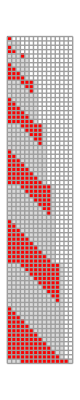
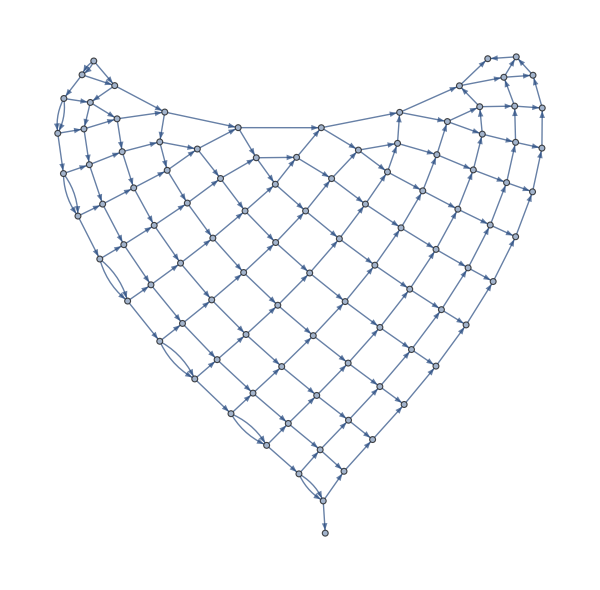
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss01=SSS[rs01[["RuleSet"]], "B",500,
 SSSMax->75,NetMax->100,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,338.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic];
```

```mathematica
sss01[["Net"]]//Short
```

{1→2,1→2,2→3,1→3,2→4,4→5,«971»,497→498,468→498,498→499,469→499,499→500,470→500}

```mathematica
nds01=ToNetDifferenceSets[sss01[["Net"]]]
```

{{1,1,2},{1,2},{2,6},{1,2,2},{2,3},{1,4},{1,4},{1,4},{4,10},{1,4,4},{1,4},{1,4},{4,5},{1,6},{1,6},{1,6},{1,6},{1,6},{6,14},{1,6,6},{1,6},{1,6},{1,6},{1,6},{6,7},{1,8},{1,8},{1,8},{1,8},{1,8},{1,8},{1,8},{8,18},{1,8,8},{1,8},{1,8},{1,8},{1,8},{1,8},{1,8},{8,9},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10,22},{1,10,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10,11},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12,26},{1,12,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12,13},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{14,30},{1,14,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{14,15},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{16,34},{1,16,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{16,17},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{18,38},{1,18,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{18,19},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{20,42},{1,20,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{20,21},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{22,46},{1,22,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{22,23},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{24,50},{1,24,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{24,25},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{26,54},{1,26,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{26,27},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{28,58},{1,28,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{28,29},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{30},{1,30,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
rslo1=ReduceSetList[nds01]
```

{{1,1,2},{1,2},{2,6},€_(n$2⊨1)^6[{1,-2+4 n$2,-2+4 n$2},€_(n$1⊨1)^2[€^(-7+3 n$1+4 n$2)[{1,-4+2 n$1+4 n$2}],{-4+2 n$1+4 n$2,-4+3 n$1+4 n$1 n$2}],{1,4 n$2,4 n$2},€_(n$1⊨1)^2[€^(-5+3 n$1+4 n$2)[{1,-2+2 n$1+4 n$2}],{-2+2 n$1+4 n$2,-4+5 n$1+4 n$1 n$2}]],{1,26,26},€_(n$1⊨1)^2[€^(24+3 (-1+n$1))[{1,26+2 (-1+n$1)}],{26+2 (-1+n$1),27+31 (-1+n$1)}],{1,28,28},€^26[{1,28}],{28,29},€^29[{1,30}],{30},{1,30,30},€^18[{1,30}],€^10[{1}],{},€^18[{1}]}

```mathematica
€_(n$1⊨1)^2[€^(-7+3 n$1+4 n$2)[{1,-4+2 n$1+4 n$2}],{-4+2 n$1+4 n$2,-4+3 n$1+4 n$1 n$2}]
```

### Code

#### Code for sessies

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["SSS`"];
```

#### Code to display and evaluate/expand normal and indexed concatenation

```mathematica
Concatenate[l__List] := Join[l];
Format[Concatenate[l__]] := Row[Riffle[{l},"⧺"]];  (* FromCharacterCode[10746] *)
```

```mathematica
Clear[IndexedConcatenate];
Format[IndexedConcatenate[x__, {var_, start_, finish_}]] :=
DisplayForm[RowBox[{UnderoverscriptBox["€", RowBox[{var,"⊨", start}], finish], "[", Sequence @@ Riffle[{x}, ","], "]"}]];  (* FromCharacterCode[8364] *)
Format[IndexedConcatenate[x__, {var_, finish_}]] :=  DisplayForm[RowBox[{UnderoverscriptBox["€", var, finish], "[", Sequence @@ Riffle[{x}, ","], "]"}]];
Format[IndexedConcatenate[x__, finish_]] := DisplayForm[RowBox[{OverscriptBox["€", finish], "[", Sequence @@ Riffle[{x}, ","], "]"}]];
```

```mathematica
iC[x__, iter:(_Integer|{_,_Integer}|{_,_Integer,_Integer})]:= Sequence @@ (Join @@ Table[{x},  iter]); 
(* allow 1 or more elements to be repeated & concatenated according to iter, result will be a subsequence, assumed to be inside a List *)
iC[x__] := IndexedConcatenate[x] (* any non-resolved cases redefined, awaiting further processing *)

Unprotect[Expand,ExpandAll];
ExpandAll[x_ /; !FreeQ[x,IndexedConcatenate]] := (x //. IndexedConcatenate->iC);
Expand[x_ /; !FreeQ[x,IndexedConcatenate] ] := (x /. IndexedConcatenate->iC);
Protect[Expand,ExpandAll];
```

#### Code to convert a network to/from its specification as a list of sets of integers, and compact it

```mathematica
ToNetDifferenceSets::usage ="ToNetDifferenceSets[net] takes a network given as a list of rules and returns a list of difference sets (sets of link lengths for each node) describing the same network.  A set {n1, n2, ...} in position i indicates that net contained edges {i->n1, i->n2, ...}.";
FromNetDifferenceSets::usage ="FromNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns the network described.  A set {n1, n2, ...} in position i of l corresponds to {i->n1, i->n2, ...} in the network.";
```

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;
Rest /@ 
Map[Last, 
Gather[Join[{#,0}& /@Range[Max[First/@nodediffpairs]],nodediffpairs],First[#1]==First[#2]&],
{2}]
];
```

```mathematica
FromNetDifferenceSets[diffs:{__List}] := Flatten[MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
```

#### Code to (attempt to) reduce lists to (nested) indexed concatenations

```mathematica
$debug=False;
```

```mathematica
ReduceSetList::usage ="ReduceSetList[l] takes a list l of elements or nested lists of elements, and summarizes duplicate elements and duplicate subsequences using DoConcatenate objects, having the format €_(var=start)^finish[...], specifying how many times the elements or subsequences are repeated.";
```

```mathematica
Clear[FindSeqFns];
FindSeqFns[repLen_Integer,varName_,subseqList_List] := Module[{parted,firstRep,numArray,fnList,ans},
If[$debug && "N"===Input["Continue? (Y/N)"],Abort[]];
parted=Partition[subseqList,repLen];
firstRep=First@parted;
If[$debug,Print["Entering FindSeqFns with:\n parted: ",parted,"\n firstRep: ",firstRep]];
numArray = Transpose[Cases[#,_Integer,∞]& /@ parted];
If[$debug,Print["\nNumerical Table to fit:\n",Grid@Transpose@numArray]];
fnList=FindSequenceFunction[#,varName]& /@ numArray;

If[$debug,Print["Function list: ",fnList];  Print[parted, " : ",firstRep];  Print@Position[firstRep,_Integer]; 
Print[ReplacePart[firstRep,Thread[Position[firstRep,_Integer] -> fnList]]]];
ans={IndexedConcatenate[Sequence@@ReplacePart[firstRep,Thread[Position[firstRep,_Integer] -> fnList]],{varName,1,Length[subseqList]/repLen}]};
If[$debug,
Print["ans: ",ans]; 
Print["ExpandAll[ans]: ",ExpandAll[ans]]; 
Print["ExpandAll[subseqList]: ",ExpandAll[subseqList]];
Print@If[ExpandAll[ans]===ExpandAll[subseqList],"(same)","(different)"]
];

If[ExpandAll[ans]===ExpandAll[subseqList],ans,subseqList]
];
```

```mathematica
improveReduction[l_List] := Module[{l1=l,l0=l,p},
If[$debug && "N"===Input["Continue? (Y/N)"],Abort[]];

If[$debug,Print["Entering improveReduction with: ",l]];
If[Length[l]<=1,
If[$debug,Print["Immediate Return"]];
Return[l]
];
p=Flatten@Position[l0,IndexedConcatenate[__,{__}],{1}]; (* find parts that might allow improved reduction *)
(* this only fits indexed concatenate objects with iterators in {...} *)
While[Length[p]>0 && Length[l0]>1,
If[$debug,Print["Trying to improve reduction at pos: ",First[p], " (of ",p,")\nLength[p] = ",Length[p],", Length[l0] = ",Length[l0]]];
l1=improveReductionAt[First[p],l0];
 (* try reducing based on (pos of) first DoConcatentate object *)
If[l1===l0, (* nothing changed, that didn't help *)
p=Rest[p], (* drop first location, try next *)
If[$debug,Print["improvement (p was ",p,"): ",l1]];
l0=l1; p=Flatten@Position[l0,IndexedConcatenate[__,{__}],{1}]; (* if improved, restart from top *)
]; (* end If *)
]; (* end While *)
l1  (* this is now the best we can do *)
];
```

```mathematica
improveReductionAt[k_Integer,l_List] :=
(* Assuming that there is a IndexedConcatenate object at position k in l, "roll" the contents to check that it can actually apply to elements immediately to its left, continuing until it fails. This should pick up cases like €^0[___], which can't be identified otherwise. *) 
Module[{wholeL,leftL,midEl,rightL,leftLNew,midElNew,rightLNew,leftEltsToDrop,temp,countRolled=0,rollLen,oldArgList,newArgList,iter,iterVar,iterStart,iterStop},
If[k<1||k>Length[l],Print["Error using k=",k,", l=",l];Abort[]];
wholeL=ExpandAll@l;
leftL= Take[l,k-1];                       (* l[[;;k-1]] *)
midEl=l[[k]];
rightL=Drop[l, k];                    (* l[[k+1;;]] *)

If[Head[midEl]=!=IndexedConcatenate,Print["Error: improveReduction called erroneously!"];Break[]
];

While[
(* we'll RollRight the midEl arguments before the iterator, drop the last elt of leftL, prepend an elt to rightL, check against wholeL, and track the countRolled. *)

If[$debug,Print["Before roll attempt: ",wholeL]];

If[Length[leftL]==0,
If[$debug,Print["No further rolling possible, we're at beginning"]];
Break[] (* out of this While loop *)
];
leftLNew =leftL;

oldArgList = Most[List@@midEl];
iter = Last[List@@midEl];
If[Length[iter]==2,iterStart=1,(* if 3 *) iterStart=iter[[2]]];
iterVar=First[iter];
iterStop=Last[iter];

newArgList = RotateRight[oldArgList];  (* roll arg list *)newArgList[[1]] = (newArgList[[1]] /. iter[[1]] ->iter[[1]]-1); (* adj 1st *)
newArgList=FullSimplify[newArgList];

If[$debug,Print["oldArgList: ",oldArgList]];
If[$debug,Print["iter: ",iter," : \n iterVar = ",iterVar,"\n iterStart = ",iterStart,"\n iterStop = ",iterStop]];
If[$debug,Print["newArgList: ",newArgList]];

leftEltsToDrop = ExpandAll@{First[newArgList] /. iterVar -> iterStart};

If[$debug,Print["leftEltsToDrop: ",leftEltsToDrop]];

While[ (* condition is whether we can shift the midEl one space to the left or not giving the same result *)
Length[leftEltsToDrop]>0 && Length[leftLNew]>0 &&
Length[(temp={ExpandAll[Last[leftLNew]]})] <= Length[leftEltsToDrop], 
If[$debug,Print["old value of leftLNew: ",leftLNew]];
leftLNew=Most[leftLNew];                                                                (* drop one term from the leftLNew *)
If[$debug,Print["new value of leftLNew: ",leftLNew]];
If[$debug,Print["dropping last ",Length[temp]," element(s) from leftEltsToDrop: ",leftEltsToDrop]];
leftEltsToDrop = Drop[leftEltsToDrop,-Length[temp]]; 
(* drop the right number of elements from (expanded) list *)
If[$debug,Print["new leftEltsToDrop: ",leftEltsToDrop]];
];
midElNew= IndexedConcatenate[Sequence@@newArgList, iter];
rightLNew = Prepend[rightL,(Last[oldArgList] /. iterVar ->iterStop)]; (* adj 1st *)

countRolled++; (* how many times did we successfully "roll" it? *)

If[$debug,Print["leftLNew: ",leftLNew,"\nMidElNew: ",midElNew,"\nrightLNew: ",rightLNew,"\n"]];
(* note that midElNew is just the element IndexedConcatenate, not a subsequence! *)
If[$debug,Print["countRolled: ",countRolled,"\n"]];

If[$debug,
If[wholeL=!=ExpandAll[Join[leftLNew ,{midElNew},rightLNew]],
Print["roll gives different result: "];
Print["wholeL: ",wholeL];
Print["leftLNew: ",leftLNew,"\nMidElNew: ",midElNew,"\nrightLNew: ",rightLNew];
Print["new stuff: ",Join[leftLNew ,{midElNew},rightLNew]];
Print["ExpandAll[new stuff]: ",ExpandAll[Join[leftLNew ,{midElNew},rightLNew]]],
Print["roll gives same result"]
]
];
wholeL===ExpandAll[Join[leftLNew ,{midElNew},rightLNew]], 
(* While condition, if it worked, try it again! *)
leftL=leftLNew;
midEl=midElNew;
rightL=rightLNew
];
(* We drop out of the While when the Roll didn't work, so our best answer is: *)
countRolled--; (* back off the count, and we'll use previous leftL, midEl, rightL *)

If[$debug,Print["Farthest left: ",Join[leftL,{midEl},rightL]]];

(* Now find how many elements we can drop from rightL if the index max is increased *)
 
midElNew=midEl;      (* revert, last roll didn't work *)
rightLNew=rightL;   (* revert both *)
newArgList = oldArgList = Most[List@@midEl]; (* revert arg list, too! *)

If[countRolled>=(rollLen=Length[newArgList]),  (* length of indexed subsequence *)
iterStop+=Quotient[countRolled,rollLen];  (* incr iterStop *)
midElNew= IndexedConcatenate[Sequence@@newArgList, {iterVar,iterStart,iterStop}];
(* change index max by # full subseqs *)
If[$debug,Print["dropping ",rollLen * Quotient[countRolled,rollLen]," elements from rightLNew: ",rightLNew]];
rightLNew=Drop[rightLNew,rollLen * Quotient[countRolled,rollLen]];  (* drop any full subsequences *)
countRolled -= rollLen * Quotient[countRolled,rollLen];
];
If[$debug,
Print["countRolled: ",countRolled];
Print["midElNew: ",midElNew];
Print["rightLNew: ",rightLNew]
];

rightLNew = SequenceReplace[rightLNew, {IndexedConcatenate[a_,iter1_], IndexedConcatenate[a_,iter2_]}:>
Which[
Head[iter1]===Head[iter2]===Integer, (* reps, no varName *)
List@IndexedConcatenate[a,iter1+iter2],
Head[iter1]===Integer && MatchQ[iter2,{varName_,__Integer}],
List@IndexedConcatenate[a,iter2[[;;-2]] ~Join~ iter2[[3]]+iter1],
Head[iter2]===Integer && MatchQ[iter1,{varName_,__Integer}],
List@IndexedConcatenate[a,iter1[[;;-2]] ~Join~ iter1[[3]]+iter2],
True,
{IndexedConcatenate[a,iter1], IndexedConcatenate[a,iter2]} (* no help! *)
]
]; (* merge neighbors if... *)

If[$debug,
Print["countRolled: ",countRolled];
Print["rightLNew: ",rightLNew]
];

(* check whether we might still have a subsequence from pieces left in rightL *)

While[ (* length possible and it matches *)
rollLen<=Length[rightLNew] && 
(temp=(newArgList /. iterVar-> iterStop+1))===rightLNew[[;;Length[temp]]],
iterStop++;
If[$debug,Print["incrementing iterStop: ", iterStop]];
midElNew= IndexedConcatenate[Sequence@@newArgList, {iterVar,iterStart,iterStop}];
If[$debug,Print["dropping ",rollLen," elements from rightLNew: ",rightLNew]];
rightLNew=Drop[rightLNew,rollLen]; (* drop one subseq from rightLNew *)
];

If[$debug,
Print["midElNew: ",midElNew];
Print["rightLNew: ",rightLNew];
];

Join[leftL,{midElNew},rightLNew]  (* leftL won't have changed, but maybe midElNew & rightLNew have *)
];
```

```mathematica
ReduceSetList[l_List]:=Module[{l1,l0=l,gl0,repLen,repMax,pos,varName,i,x,p,len},
If[$debug && "N"===Input["Continue? (Y/N)"],Abort[]];

If[$debug,Print["Entering ReduceSetList with: ",l]];
If[Length[l]<=1,
If[$debug,Print["Immediate Return"]];
Return[l]
];

(* first check for subsequences of duplicate elements *)

len=Length[l0];
l1=SequenceReplace[l0,
{x:Repeated[a_,{2,len}]}:>IndexedConcatenate[a,Length[{x}]]
]; (* looks for an exactly repeated subsequence *)

If[l1 =!= l0,(* not same, repLen 1 worked *)
If[$debug,Print["exact repLen = 1: ",l1]];
l1=improveReduction[l1];
If[$debug,Print["improved? : ",l1]];
l1=ReduceSetList[l1];
Return[l1]; 
(* if changed, call recursively to continue trying *)
];

If[$debug,Print["exact repLen: ",1]]; (* report what we tried *)
repLen = 2; (* start with length of repeating unit = 2, up to max useful *)
l0=l1; (* set up to check next attempted reduction *)
While[2 repLen <= (len=Length[l1]),
If[$debug,Print["exact repLen: ",repLen]];
l1=SequenceReplace[l1,
{x:Repeated[PatternSequence@@Table[ToExpression[ToString@Unique[x]<>"_"],{repLen}],{2,∞}]}:>
IndexedConcatenate[Sequence@@Take[{x},repLen],Length[{x}]/repLen]
];
If[l1 =!= l0,
If[$debug,Print["Changed (in While): exact repLen = ",repLen,": ",l1]];
l1=improveReduction[l1];
If[$debug,Print["improved? : ",l1]];
l1=ReduceSetList[l1];
If[$debug,Print["reduced? : ",l1]];
Return[l1]
];
(* if changed, call recursively to continue reduction, else try next repLen *)
repLen++;
];
If[$debug,Print["Exiting While[...replen...]"]];

If[l1 =!= l0,
If[$debug,Print["Changed: exact repLen = ",repLen,": ",l1]];
l1=improveReduction[l1];
If[$debug,Print["improved? : ",l1]];
l1=ReduceSetList[l1];
If[$debug,Print["reduced? : ",l1]];
Return[l1]
];(* if changed, call recursively to continue trying, else try the generic list *)

If[$debug,Print["Treating Generic patterns"]];

repLen = 1;            (* first time choice *)
l0={};                     (* force one time through loop *)

While[l1=!=l0 && Length[l1]>1, (* while changed, and of course, the first time *)
l0=l1;
If[$debug,Print["orig: ",l0]];
len=Length[l0];

gl0=(l0 /. (i_Integer /; i!=1) ->0);

If[$debug,Print["generic: ",gl0]];

pos=SequencePosition[gl0,{Repeated[PatternSequence[x_],{2,len}]},Overlaps->False];
If[$debug,Print["generic repLen: ", repLen,", pos: ",pos]];

While[Length[pos]==0 && Length[l0]>1 &&Length[l0]>2*(repLen+1),
repLen++;
pos=SequencePosition[gl0,{Repeated[PatternSequence@@Table[ToExpression[ToString@Unique[x]<>"_"],{repLen}],{2,∞}]},Overlaps->False];
If[$debug,Print["generic repLen: ", repLen,", pos: ",pos]];
];

If[pos==0,
If[$debug,Print["Returning, no generic matches found"]];
Return[l0]];  (* No further reduction found *)

(* at least one possible reduction found *)

Do[     (* find first unused variable name of form n$i, where i is an integer *)
varName=ToExpression["n$"<>ToString[i]];
If[FreeQ[l0,varName],Break[]],
{i,1,∞}];

If[$debug,Print["new varName: ",varName]];

l1=Flatten[SequenceSplit[l0,Thread[(Take[l0,#]& /@ pos) -> (FindSeqFns[repLen,varName,Take[l0,#]]& /@ pos)]],1];
If[l1=!=l0, 
If[$debug,Print["generic repLen = ",repLen,": ",l1]];
l1=improveReduction[l1];
If[$debug,Print["improved? : ",l1]];
];
]; (* end of While l1≠l0 loop *)

l1 (* here l1==l0, best we can do *)
];
```